```mathematica
x[t_]:=Cos[(2*Pi*n*(t-shift1))/T]Exp[-((m(t-shift1))/T)^2]
y[t_]:=Cos[(2*Pi*n*(t-shift2))/T]Exp[-((m(t-shift2))/T)^2]
```

```mathematica
m=10; n=9;
Integrate[x[t]*y[t]/T, {t, 0, T}]
```

1/(8 m)ⅇ^(-(2 n^2 π^2)/m^2-(m^2 (shift1-shift2)^2)/(2 T^2)) √(π/2) (2 ⅇ^((2 n^2 π^2)/m^2) Cos[(2 n π (-shift1+shift2))/T] Erf[(m (shift1+shift2))/(√2 T)]-2 ⅇ^((2 n^2 π^2)/m^2) Cos[(2 n π (-shift1+shift2))/T] Erf[(m (shift1+shift2-2 T))/(√2 T)]-Erf[(-m^2 (shift1+shift2)-2 ⅈ n π T)/(√2 m T)]+Erf[(m^2 (shift1+shift2)-2 ⅈ n π T)/(√2 m T)]+Erf[(-m^2 (shift1+shift2-2 T)-2 ⅈ n π T)/(√2 m T)]-Erf[(m^2 (shift1+shift2-2 T)-2 ⅈ n π T)/(√2 m T)])

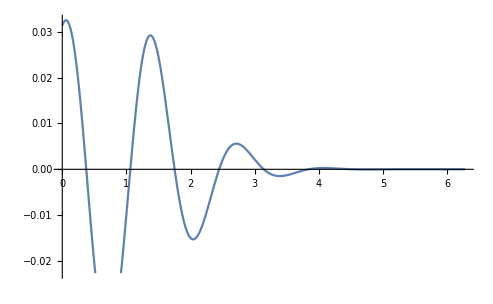

```mathematica
m=10; n=9; shift1=0; T=4*Pi;
Plot[1/(8 m)ⅇ^(-(2 n^2 π^2)/m^2-(m^2 (shift1-shift2)^2)/(2 T^2)) √(π/2) (2 ⅇ^((2 n^2 π^2)/m^2) Cos[(2 n π (-shift1+shift2))/T] Erf[(m (shift1+shift2))/(√2 T)]-2 ⅇ^((2 n^2 π^2)/m^2) Cos[(2 n π (-shift1+shift2))/T] Erf[(m (shift1+shift2-2 T))/(√2 T)]-Erf[(-m^2 (shift1+shift2)-2 ⅈ n π T)/(√2 m T)]+Erf[(m^2 (shift1+shift2)-2 ⅈ n π T)/(√2 m T)]+Erf[(-m^2 (shift1+shift2-2 T)-2 ⅈ n π T)/(√2 m T)]-Erf[(m^2 (shift1+shift2-2 T)-2 ⅈ n π T)/(√2 m T)]), {shift2, 0, 2*Pi}]
```